```mathematica
numOfSolTarget=4*^6;
```

At the most pc prime factors are needed in order for the total number of unique solutions to DR equation to exceed c.

```mathematica
primeFactorCountMax=Ceiling[Log[3,numOfSolTarget]]
```

15

```mathematica
numberOfSquaredPrimeFactorMax=Ceiling[Log[5,numOfSolTarget]]
```

10

```mathematica
numOfSolFactor1=Product[2exponet[i]+1,{i,1,numberOfSquaredPrimeFactorMax}]
```

(1+2 exponet[1]) (1+2 exponet[2]) (1+2 exponet[3]) (1+2 exponet[4]) (1+2 exponet[5]) (1+2 exponet[6]) (1+2 exponet[7]) (1+2 exponet[8]) (1+2 exponet[9]) (1+2 exponet[10])

```mathematica
contributionThreashold=100;
While[
Floor[Log[Prime[numberOfSquaredPrimeFactorMax],contributionThreashold]]<2,
contributionThreashold*=2
];
contributionThreashold
```

1600

```mathematica
Table[{exponet[i],0,Floor[Log[Prime[i],400]]},{i,1,numberOfSquaredPrimeFactorMax}]
```

{{exponet[1],0,8},{exponet[2],0,5},{exponet[3],0,3},{exponet[4],0,3},{exponet[5],0,2},{exponet[6],0,2},{exponet[7],0,2},{exponet[8],0,2},{exponet[9],0,1},{exponet[10],0,1}}

```mathematica
Product[Prime[i]^exponet[i],{i,1,7}]
```

2^exponet[1] 3^exponet[2] 5^exponet[3] 7^exponet[4] 11^exponet[5] 13^exponet[6] 17^exponet[7]

```mathematica
arr=With[
{iterator=Sequence@@Table[{exponet[i],0,Floor[Log[Prime[i],contributionThreashold]]},{i,1,numberOfSquaredPrimeFactorMax}]},
Flatten[
Table[
{ 
Product[2exponet[i]+1,{i,1,numberOfSquaredPrimeFactorMax}],
Product[Prime[i]^exponet[i],{i,1,numberOfSquaredPrimeFactorMax}]
},
iterator
],
Floor[numberOfSquaredPrimeFactorMax]-1
]
];
```

```mathematica
Length[arr]
```

1496880

```mathematica
arr//RandomChoice
```

{209475,13060642154560000}

```mathematica
work[{numberOfSolutionFactor1_, currentN_}]:= Module[
{num=Ceiling[Log[3,2*numOfSolTarget/numberOfSolutionFactor1]]}, currentN Product[Prime[i],{i,Floor[numberOfSquaredPrimeFactorMax]+1,Floor[numberOfSquaredPrimeFactorMax]+num}]]
```

```mathematica
Map[work,arr]//Min
```

9350130049860600

Answer: 9350130049860600

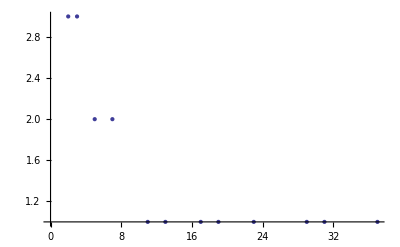

```mathematica
ListPlot[FactorInteger[9350130049860600]]
```